## RNN Sequence 10

```mathematica
mldata=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\mldata.wxf"];
```

```mathematica
columnHeads=v/@{"timeStep","temperature","BusinessDay","Lag1","Lag2","Lag3","Lag4","Lag5","Lag6","Lag7","Lag8","Lag9","Lag10","Lag11","Lag12","Lag13","Lag14","Lag15","Lag16","Lag17","Lag18","Lag19","Lag20","Lag21","Lag22","Lag23","Lag24","Lag25","Lag26","Lag27","Lag28","Lag29","Lag30","Load"}
```

```mathematica
mldataAssocs=AssociationThread[{"timeStep","temperature","BusinessDay","Lag1","Lag2","Lag3","Lag4","Lag5","Lag6","Lag7","Lag8","Lag9","Lag10","Lag11","Lag12","Lag13","Lag14","Lag15","Lag16","Lag17","Lag18","Lag19","Lag20","Lag21","Lag22","Lag23","Lag24","Lag25","Lag26","Lag27","Lag28","Lag29","Lag30","Load"}->#]&/@mldata;
```

```mathematica
mldataAssocs[[50]]
```

<|timeStep→79.,temperature→10.6,BusinessDay→1,Lag1→10719.1,Lag2→9878.77,Lag3→9625.04,Lag4→9670.69,Lag5→9879.88,Lag6→10225.5,Lag7→11432.7,Lag8→12074.8,Lag9→13270.4,Lag10→14301.6,Lag11→14871.9,Lag12→14446.4,Lag13→13936.7,Lag14→13631.3,Lag15→13469.6,Lag16→13554.3,Lag17→13686.4,Lag18→13783.5,Lag19→13648.9,Lag20→13316.6,Lag21→12717.6,Lag22→11761.4,Lag23→10711.6,Lag24→10056.5,Lag25→9814.86,Lag26→9648.07,Lag27→9658.6,Lag28→9829.64,Lag29→10148.7,Lag30→10647.3,Load→12654.9|>

```mathematica
chunkSize=10;
allDataWithTemp=(Lookup[Most[#],{"Load","temperature"}])->(Last[#][["Load"]])&/@Partition[mldataAssocs,chunkSize+1,1];
```

```mathematica
allDataWithTemp[[;;5]]
```

{{{10605.9,13.3008},{10775.7,13.3},{11856.2,13.3},{12979.6,13.2994},{13753.7,13.3},{13870.1,12.8003},{13955.2,12.2004},{13865.3,12.2},{13643.7,12.2},{13457.9,12.7996}}→13354.2,{{10775.7,13.3},{11856.2,13.3},{12979.6,13.2994},{13753.7,13.3},{13870.1,12.8003},{13955.2,12.2004},{13865.3,12.2},{13643.7,12.2},{13457.9,12.7996},{13354.2,12.8}}→13466.1,{{11856.2,13.3},{12979.6,13.2994},{13753.7,13.3},{13870.1,12.8003},{13955.2,12.2004},{13865.3,12.2},{13643.7,12.2},{13457.9,12.7996},{13354.2,12.8},{13466.1,13.2993}}→13773.,{{12979.6,13.2994},{13753.7,13.3},{13870.1,12.8003},{13955.2,12.2004},{13865.3,12.2},{13643.7,12.2},{13457.9,12.7996},{13354.2,12.8},{13466.1,13.2993},{13773.,13.3}}→14224.4,{{13753.7,13.3},{13870.1,12.8003},{13955.2,12.2004},{13865.3,12.2},{13643.7,12.2},{13457.9,12.7996},{13354.2,12.8},{13466.1,13.2993},{13773.,13.3},{14224.4,13.3}}→14401.8}

```mathematica
{trainingdata,testdata}=TakeDrop[allDataWithTemp,45000];
```

```mathematica
rnn=NetChain[{GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.3},"Input"->{"Varying",10}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[128],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
trainednet =  NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
nso=trainednet["TrainedNet"]
```

NetTrain::invindim3: Data provided to port "Input" should be a non-empty list of n×10 matrices of real numbers, but was a 10×2 matrix of real numbers.

$Failed

$Failed[TrainedNet]

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→367478.|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{15571.1,15650.6,15550.,15302.7,15084.7,15006.5,15040.4,15374.6,15861.4,16102.7}}→16253.8,{{11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3}}→13460.6}

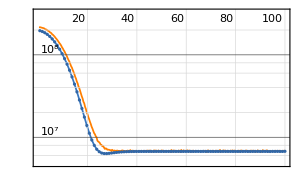
NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.9min  examples/s:12884
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:6.81×10^6
validation | ,,  loss:6.76×10^6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3}}]

```mathematica
trainednet[rsample[[2,1]]]
```

```mathematica
sobj=NetStateObject[trainednet]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

$Failed

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainedNet[#]}],1]&,testdata[[1,1]],100]
```

{11828.,109}
 |  |  |  |

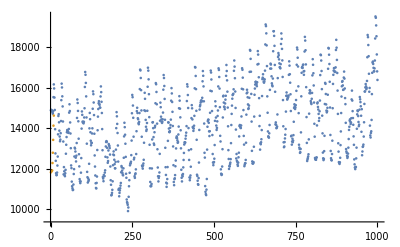

```mathematica
ListPlot[{testdata[[1;;1000,2]],results}]
```